## First the definitions

```mathematica
SymbolReplace[sym_,edge_]:=Block[{s},
s=SymbolToSets[sym];
s=Map[Sort[Flatten[(#/.edge[[1]]->{edge[[1]],edge[[2]]})]]&,s];
SetsToSymbol[s]
]
```

```mathematica
JoinGraphs[f_,g_,h_]:=Block [{edges,full},
edges=Join[
Table[e->Directive[{Thick,Red}],{e,EdgeList[f]}],
Table[e->Directive[{Thick,Yellow}],{e,SetDifference[SetDifference[EdgeList[g],EdgeList[f]],EdgeList[h]]}],
Table[e->Directive[{Thick,Blue}],{e,EdgeList[h]}]
];
full=GraphUnion[f,g,h];
Graph[full,VertexLabels->Table[v->If[SymbolLevel[v]==4,Rotate[Framed[SymbolToLabel[v],FrameStyle->Directive[Red,Thin]],Pi/6],Rotate[SymbolToLabel[v],Pi/6]],{v,VertexList[full]}],EdgeStyle->edges,
VertexStyle->Join[
Table[v->Red,{v,VertexList[f]}],
Table[v->Blue,{v,VertexList[h]}]],
GraphLayout->"LayeredDigraphEmbedding",
ImageSize->400
]
]
```

```mathematica
FindFullFormula12345[g_]:=Block[{},
Monitor[
formulaDepth=0;FindFullFormula12345[g,Table[{v},{v,VertexList[g]}]],
formulaDepth
]
]
```

```mathematica
FindFullFormula12345[g_,v_]:=Block[{edge,pos1,pos2,v2,result={},result1,result2,clique},
If[CompleteGraphQ[g],
result=Select[{SetsToSymbol2[Sort[Map[Sort[#]&,v],#1[[1]]<#2[[1]]&]]},SymbolLevel[#]≤5&]
,
clique=First[FindClique[g]];
If[Length[clique]≤5,
edge=First[EdgeList[GraphComplement[g]]];
Table[If[MemberQ[v[[k]],edge[[1]]],pos1=k],{k,Length[v]}];
Table[If[MemberQ[v[[k]],edge[[2]]],pos2=k],{k,Length[v]}];
v2=v;
v2[[pos1]]=Join[v2[[pos1]],v2[[pos2]]];
v2=Delete[v2,pos2];
result=Join[
FindFullFormula12345[EdgeAdd[g,edge],v],
FindFullFormula12345[VertexContract[g,{edge[[1]],edge[[2]]}],v2]
]
,
{}
]
];
If[Length[result]>formulaDepth,formulaDepth=Length[result]];
result
]
```

```mathematica
HandleGraph[g_]:=Block[{edges,full},
edges=DeleteDuplicates[EdgeList[g],IsomorphicGraphQ[EdgeContract[g,#1],EdgeContract[g,#2]]&];
edges=EdgeList[g];
Monitor[
{Graph[g,VertexLabels->"Name"],
Table[With[{
without=Graph[VertexList[EdgeDelete[g,e]],EdgeList[EdgeDelete[g,e]],VertexLabels->"Name",GraphHighlight->{e[[1]],e[[2]]},GraphHighlightStyle->"Thick",GraphLayout->"TutteEmbedding", ImageSize->50],
contract =Graph[EdgeList[EdgeContract[g,e]],VertexLabels->"Name",GraphHighlight->{e[[1]]},GraphHighlightStyle->"Thick",GraphLayout->"TutteEmbedding", ImageSize->50],
with=Graph[VertexList[g],EdgeList[g],GraphHighlight->e,GraphLayout->"TutteEmbedding", VertexLabels->"Name",GraphHighlightStyle->"Thick",ImageSize->50]
},
Labeled[
Graph[
JoinGraphs[
FormulaGraphReverse2[FindFullFormula[g]],
FormulaGraphReverse2[FindFullFormula[without]],
FormulaGraphReverse2[Map[SymbolReplace[#,e]&,FindFullFormula[contract]]]
],ImageSize->400
],
{
e,
Yellow->{"Without",ChromaticPolynomial[without,4]/24,without},
"==",
Red->{"With",ChromaticPolynomial[g,4]/24,with},
Blue->{"Contract",ChromaticPolynomial[contract,4]/24,contract}
}
]
],{e,edges}]
},
e]
]
```

## Then some samples

```mathematica
allGraphs5[amigo1,"graph"]
```

-Graphics-

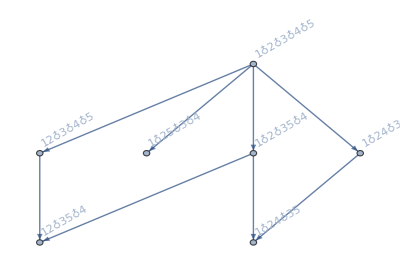
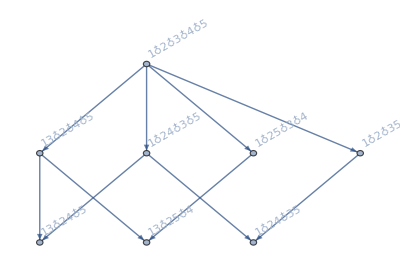
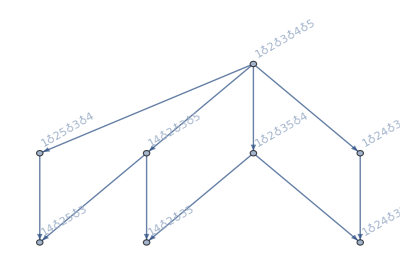
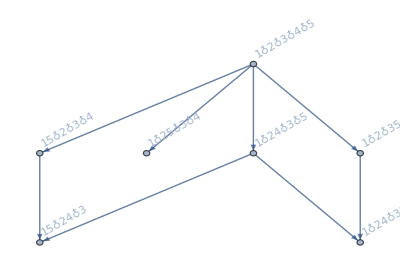
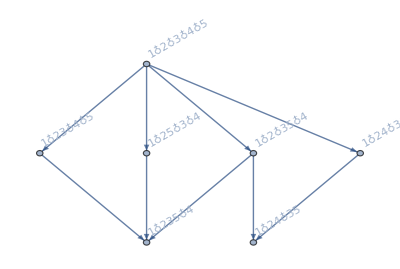
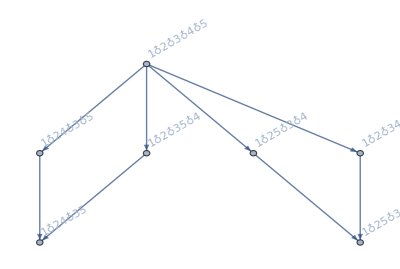
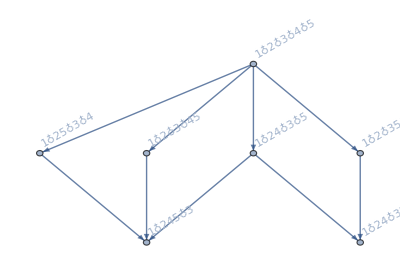
{-Graphics-,{-Graphics-{1<->2,RGBColor[1, 1, 0]→{Without,6,-Graphics-},==,RGBColor[1, 0, 0]→{With,4,-Graphics-},RGBColor[0, 0, 1]→{Contract,2,-Graphics-}},-Graphics-{1<->3,RGBColor[1, 1, 0]→{Without,7,-Graphics-},==,RGBColor[1, 0, 0]→{With,4,-Graphics-},RGBColor[0, 0, 1]→{Contract,3,-Graphics-}},-Graphics-{1<->4,RGBColor[1, 1, 0]→{Without,7,-Graphics-},==,RGBColor[1, 0, 0]→{With,4,-Graphics-},RGBColor[0, 0, 1]→{Contract,3,-Graphics-}},-Graphics-{1<->5,RGBColor[1, 1, 0]→{Without,6,-Graphics-},==,RGBColor[1, 0, 0]→{With,4,-Graphics-},RGBColor[0, 0, 1]→{Contract,2,-Graphics-}},-Graphics-{2<->3,RGBColor[1, 1, 0]→{Without,6,-Graphics-},==,RGBColor[1, 0, 0]→{With,4,-Graphics-},RGBColor[0, 0, 1]→{Contract,2,-Graphics-}},-Graphics-{3<->4,RGBColor[1, 1, 0]→{Without,6,-Graphics-},==,RGBColor[1, 0, 0]→{With,4,-Graphics-},RGBColor[0, 0, 1]→{Contract,2,-Graphics-}},-Graphics-{4<->5,RGBColor[1, 1, 0]→{Without,6,-Graphics-},==,RGBColor[1, 0, 0]→{With,4,-Graphics-},RGBColor[0, 0, 1]→{Contract,2,-Graphics-}}}}

```mathematica
HandleGraph[allGraphs5[amigo1,"graph"]]
```

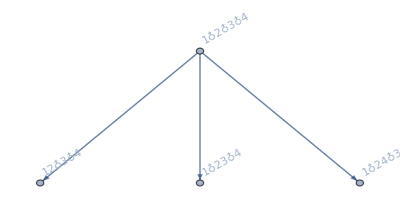
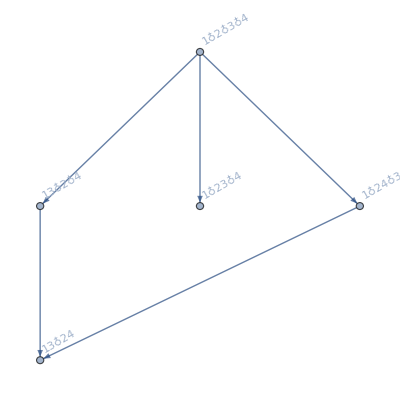
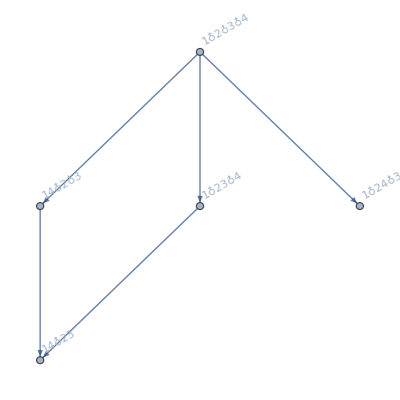
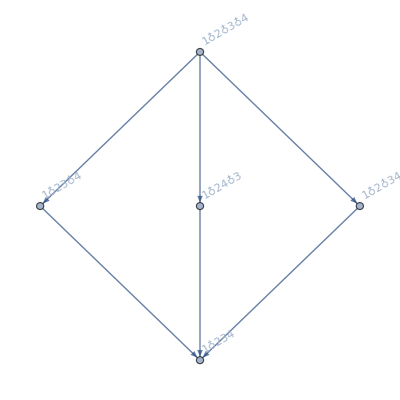
{-Graphics-,{-Graphics-{1<->2,RGBColor[1, 1, 0]→{Without,4,-Graphics-},==,RGBColor[1, 0, 0]→{With,3,-Graphics-},RGBColor[0, 0, 1]→{Contract,1,-Graphics-}},-Graphics-{1<->3,RGBColor[1, 1, 0]→{Without,9/2,-Graphics-},==,RGBColor[1, 0, 0]→{With,3,-Graphics-},RGBColor[0, 0, 1]→{Contract,3/2,-Graphics-}},-Graphics-{1<->4,RGBColor[1, 1, 0]→{Without,9/2,-Graphics-},==,RGBColor[1, 0, 0]→{With,3,-Graphics-},RGBColor[0, 0, 1]→{Contract,3/2,-Graphics-}},-Graphics-{3<->4,RGBColor[1, 1, 0]→{Without,9/2,-Graphics-},==,RGBColor[1, 0, 0]→{With,3,-Graphics-},RGBColor[0, 0, 1]→{Contract,3/2,-Graphics-}}}}

```mathematica
HandleGraph[allGraphs5[alfaKey,"graph"]]
```